```mathematica
(* See if the plots of the dispersion equation actually make sense *)
(* only consider the TE mode for now *)
(* in C++ calculation disp eqn is discontinuous across search space *)
(* this should not be the case *)
(* R. Sheehan 18 - 12 - 2020 *)
```

```mathematica
nc = 3.38; (* core RI *)
nr = 3.17; (* rib RI *)
ns=1.0; (* substrate RI *)
ncl=2.0; (* cladding RI *)
λ=1.55;(* wavelength in units of um *)
W=1;(* core width units of um *)
Dr=1.5;(* rib width units of um *)
k=(2π)/λ; (* wavenumber *)
lower=k Max[ns, ncl];(* This is required to ensure that search space will only occur over real valued functions *)
upper = k nr;
kncsqr = (k nc)^2; 
knrsqr = (k nr)^2; 
knclsqr = (k ncl)^2; 
knsqr = (k ns)^2;
```

```mathematica
p[x_]:=√(x^2-knsqr);
q[x_]:=√(x^2-knclsqr);
h[x_]:=√(kncsqr-x^2);
r[x_]:=√(knrsqr-x^2);
phase[x_,m_]:=ArcTan[q[x]/r[x]]-Dr r[x]-m π; 
F1[x_]:=p[x]/h[x];
F2[x_]:=r[x]/h[x];
F3[x_]:=Tan[phase[x,0]];
```

```mathematica
Print["h[lower]:",h[lower],", h[upper]: ",h[upper]]
Print["r[lower]:",r[lower],", r[upper]: ",r[upper]]
Print["p[lower]:",p[lower],", p[upper]: ",p[upper]]
Print["q[lower]:",q[lower],", q[upper]: ",q[upper]]
Print["ψ[lower]:",phase[lower,0],", ψ[upper]: ",phase[upper,0]]
Print["Tan[ψ[lower]]:",Tan[phase[lower,0]],", Tan[ψ[upper]]: ",Tan[phase[upper,0]]]
Print["r[lower]/h[lower]:",r[lower]/h[lower],", r[upper]/h[upper]: ",r[upper]/h[upper]]
Print["(r[lower]/h[lower])Tan[ψ[lower]]:",r[lower]/h[lower] Tan[phase[lower,0]],", (r[upper]/h[upper])Tan[ψ(upper)]: ",r[upper]/h[upper] Tan[phase[upper,0]]]
```

h[lower]:11.0453, h[upper]: 4.75421

r[lower]:9.9698, r[upper]: 0.

p[lower]:7.02116, p[upper]: 12.194

q[lower]:0., q[upper]: 9.9698

Power::infy: Infinite expression 1/0. encountered.

ψ[lower]:-14.9547, ψ[upper]: Indeterminate

Power::infy: Infinite expression 1/0. encountered.

Tan[ψ[lower]]:0.937715, Tan[ψ[upper]]: Indeterminate

r[lower]/h[lower]:0.902625, r[upper]/h[upper]: 0.

Power::infy: Infinite expression 1/0. encountered.

(r[lower]/h[lower])Tan[ψ[lower]]:0.846405, (r[upper]/h[upper])Tan[ψ(upper)]: Indeterminate

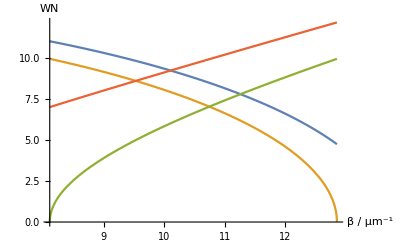

```mathematica
Plot[{h[x],r[x],q[x],p[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","WN"}]
```

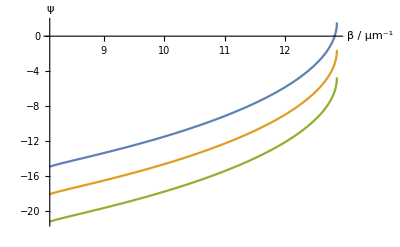

```mathematica
Plot[{phase[x,0],phase[x,1],phase[x,2]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ψ"}]
```

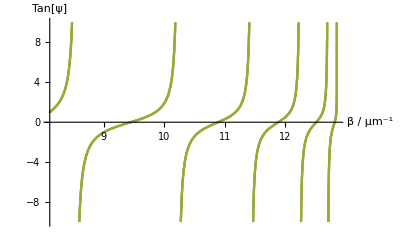

```mathematica
Plot[{Tan[phase[x,0]],Tan[phase[x,1]],Tan[phase[x,2]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Tan[ψ]"},PlotRange->{{lower, upper},{-10,10}}]
```

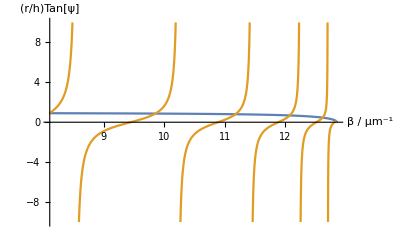

```mathematica
Plot[{(r[x]/h[x]),(r[x]/h[x])Tan[phase[x,0]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","(r/h)Tan[ψ]"},PlotRange->{{lower, upper},{-10,10}}]
```

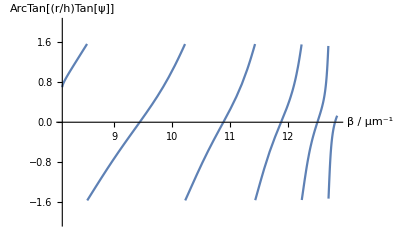

```mathematica
Plot[{ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(r/h)Tan[ψ]]"},PlotRange->{{lower, upper},{-2,2}}]
```

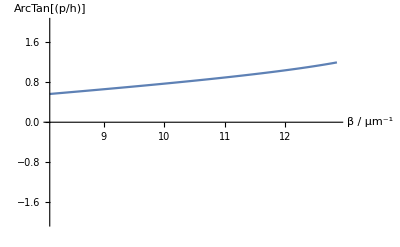

```mathematica
Plot[{ArcTan[(p[x]/h[x])]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"},PlotRange->{{lower, upper},{-2,2}}]
```

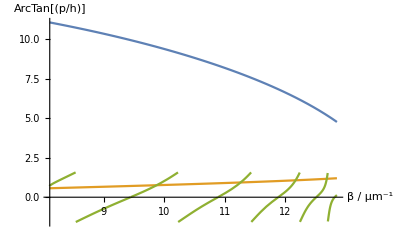

```mathematica
Plot[{W h[x],ArcTan[(p[x]/h[x])],ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

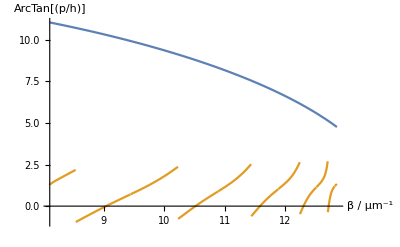

```mathematica
Plot[{W h[x],ArcTan[(p[x]/h[x])]+ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

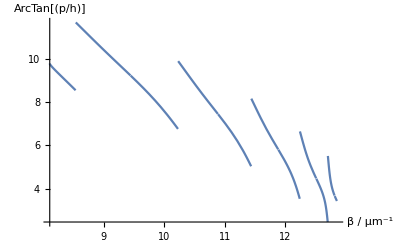

```mathematica
Plot[{W h[x]-ArcTan[(p[x]/h[x])]-ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

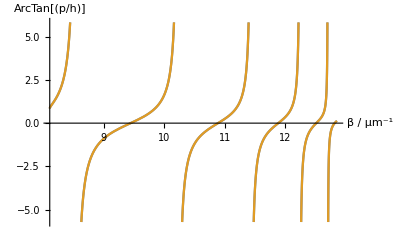

```mathematica
Plot[{(r[x]/h[x])Tan[phase[x,0]],F2[x] F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

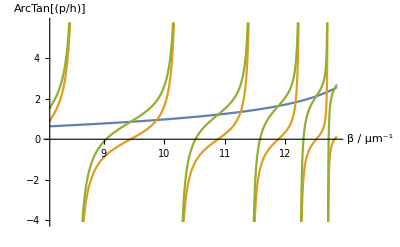

```mathematica
Plot[{F1[x],F2[x] F3[x],F1[x]+F2[x] F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

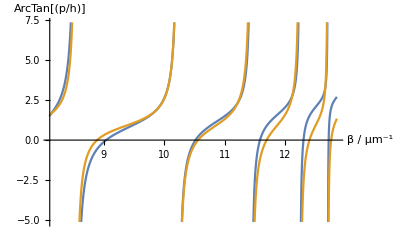

```mathematica
Plot[{F1[x]+F2[x] F3[x],1+F1[x]F2[x] F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

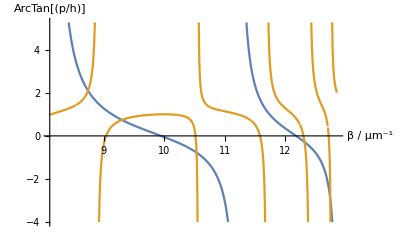

```mathematica
Plot[{Tan[W h[x]],(F1[x]+F2[x] F3[x])/(1+F1[x]F2[x]F3[x])},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

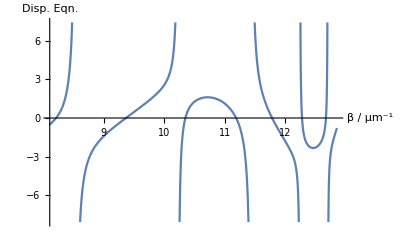

```mathematica
Plot[{Sin[W h[x]](1-F1[x]F2[x]F3[x])-Cos[W h[x]](F1[x]+F2[x]F3[x])},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Disp. Eqn."}]
```

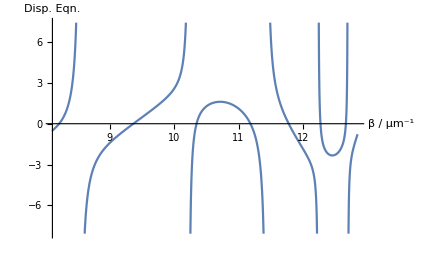

```mathematica
Plot[{Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Disp. Eqn."}]
```

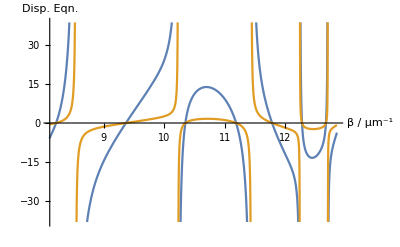

```mathematica
Plot[{h[x] Sin[W h[x]]-p[x]Cos[W h[x]]-(Cos[W h[x]]+p[x]/h[x] Sin[W h[x]])r[x]F3[x],Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Disp. Eqn."}]
```

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,9}]
```

{x→9.36541}

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,10.5}]
```

{x→10.3475}

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,11.2}]
```

{x→11.1854}

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,11.9}]
```

{x→11.7797}

```mathematica
FindRoot[ h[x]Sin[W h[x]]-p[x]Cos[W h[x]]-(Cos[W h[x]]+p[x]/h[x] Sin[W h[x]])r[x]F3[x]==0,{x,10.5}]
```

{x→10.3475}